1

Rc=0.000151516

p0=0.5

eigenState defined

ρ0[r]

ρ defined

eqn for m defined

condition for m defined

eqn for p defined

condition for p defined

p0=0.5

ρ0=0.0992126

System defined

Rstar=119850.km

Rmax=119850.km

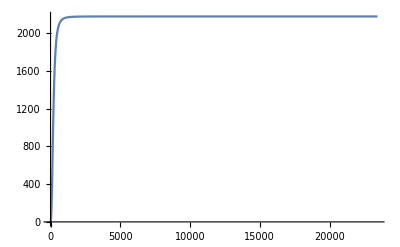

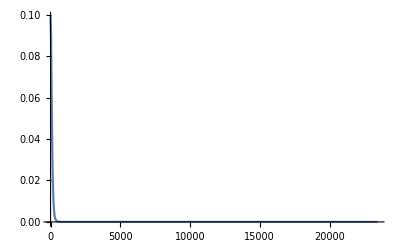

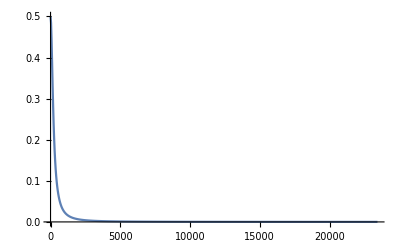

Radius=119850.

Mass=2179.02-0.00015099 ⅈ

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
(*m[r]:=4/3 π r^3 ρ0*)
my0:=10^(-4);
κ:=0.3
(*r:=ρ[x]*)
rs:=0.01;
Rsun:=1;
maxInt:=2000;
Rc:=6/(Rsun^2)*(rs/Rsun) *(1-(1-rs/Rsun)^(1/2))/(3*(1-rs/Rsun)^(1/2)-1);
bastard[x_]:=m[x]/x^2;
bastard2[x_]:=m[x]/x;
K=1
p0:=3rs/(Rc*Rsun^3)*(1-(1-rs/Rsun)^(1/2))/(3*(1-rs/Rsun)^(1/2)-1);
Print["Rc=",Rc,""];
Print["p0=",p0,""];
eqnState:={p[x]==K*ρ[x]^(κ)}
Print["eigenState defined"];
ρ[r_]=ρ0[r]
p[r_]=K*(ρ0[r])^(κ);
(*ρ[x_]:=1*)
Print["ρ defined"];
(*p[x_]=K*(ρ[x])^(κ);*)
eqnM:={m'[x]==(Rsun/rs)*(Rc*Rsun*Rsun)x^2 ρ[x]}
Print["eqn for m defined"];
(*condM:={m[my0]==0}*)
condM:={m[my0]==0}
Print["condition for m defined"];
eqnP:={-p'[x]==(rs/(2*Rsun))*(ρ[x]+p[x])*(bastard[x]+(Rsun/rs)*(Rc*Rsun*Rsun*p[x]*x))/(1-rs/Rsun * bastard2[x])}
Print["eqn for p defined"];
condP:={p[my0]==p0}
Print["condition for p defined"];
Print["p0=",p0,""];
condρ:={ρ[my0]==(p0/K)^(1/κ)}
Print["ρ0=",(p0/K)^(1/κ),""];
stopCond:={WhenEvent[Evaluate[Re[ρ0[x]]<=0],rMax=x;"StopIntegration"]}
system:=Join[eqnM,eqnP,condM,condρ, stopCond];
Print["System defined"];
state=First[NDSolve`ProcessEquations[system, {m,ρ0}, {x, my0, ∞}]];
NDSolve`Iterate[state,∞]
sol=NDSolve`ProcessSolutions[state];
rStar=Last[state@"CurrentTime"[]];
Print["Rstar=",rStar,"km"];
Print["Rmax=",rMax,"km"];
(*rMax:=maxInt*)
(*sol=NDSolve[system, {p}, {r, my0, ∞}];*)
Plot[Evaluate[m[x]/.sol],{x,my0,rMax},PlotRange->All]
Plot[Evaluate[ρ0[x]/.sol],{x,my0,rMax},PlotRange->All]
Plot[Evaluate[p[x]/.sol],{x,my0,rMax},PlotRange->All]
Print["Radius=",rMax,""];
Print["Mass=",Evaluate[m[rMax]/.sol],""];
```